## Academic plot style

```mathematica
(* =Academic Plot Theme=*)
Begin["System`PlotThemeDump`"];
Themes`ThemeRules;(*preload Theme system*)(*Define the base theme*)resolvePlotTheme["Academic",def:_String]:=Themes`SetWeight[Join[resolvePlotTheme["AcademicFrame",def],(*Axes feature*)resolvePlotTheme["Figure",def],(*Size feature*)resolvePlotTheme["HeavyLines",def],(*Curve thickness feature*)resolvePlotTheme["VividColor",def],(*Color feature*)resolvePlotTheme["SmallOpenMarkers",def]],(*Point marker feature*)Themes`$DesignWeight];

(* ==Axes feature==*)
(* ===2D Plots===*)
resolvePlotTheme["AcademicFrame",def:_String]:=Themes`SetWeight[Join[{Axes->False,Frame->True},(*Academic figures are framed by default*)resolvePlotTheme["AcademicFrame2D",def]],$ComponentWeight];

resolvePlotTheme["AcademicFrame",def:"PairedBarChart"|"PairedHistogram"]:=Themes`SetWeight[Join[{Axes->True,Frame->True},(*Cases with axes also*)resolvePlotTheme["AcademicFrame2D",def]],$ComponentWeight];

resolvePlotTheme["AcademicFrame",def:"ArrayPlot"|"MatrixPlot"]:=Themes`SetWeight[Join[(*Frame not specified but MeshStyle specified to be thin and light*){MeshStyle->Directive[AbsoluteThickness[0.5],Opacity[0.25]]},resolvePlotTheme["AcademicFrame2D",def]],$ComponentWeight];

resolvePlotTheme["AcademicFrame",def:"BarChart"|"PieChart"|"RectangleChart"|"SectorChart"|"CandlestickChart"|"KagiChart"|"LineBreakChart"|"PointFigureChart"|"RenkoChart"|"InteractiveTradingChart"|"TradingChart"|"NumberLinePlot"|"TimelinePlot"]:=resolvePlotTheme["AcademicFrame2D",def];(*Charts not framed*)(* ===3D Plots===*)resolvePlotTheme["AcademicFrame",def:_String/;StringMatchQ[def,___~~"3D"]]:=Themes`SetWeight[Join[{Axes->True,AxesEdge->{{-1,-1},{1,-1},{-1,-1}},Boxed->{Left,Bottom,Back}},(*Front axes back box*)resolvePlotTheme["AcademicFrame3D",def]],$ComponentWeight];

resolvePlotTheme["AcademicFrame","ChromaticityPlot3D"]:=Themes`SetWeight[Join[{Axes->True,AxesEdge->{{-1,-1},{-1,-1},{-1,1}},Boxed->{Left,Top,Front}},(*Front box back axes*)resolvePlotTheme["AcademicFrame3D","ChromaticityPlot3D"]],$ComponentWeight];

resolvePlotTheme["AcademicFrame",def:"BarChart3D"|"PieChart3D"|"RectangleChart3D"|"SectorChart3D"]:=resolvePlotTheme["AcademicFrame3D",def];(*Chart3Ds not boxed*)(* ===Common features of axes/frame===*)(*Mathematica's working theme:axes and frames too thin,terribly grayish,and tick/label font too small,but grids too thick.The new theme will fix these.*)resolvePlotTheme["AcademicFrame2D",_]:=Themes`SetWeight[{AxesStyle->Directive[AbsoluteThickness[1],monoColor,FontSize->14],FrameStyle->Directive[AbsoluteThickness[1],monoColor,FontSize->14],TicksStyle->Directive[monoColor,FontSize->12],FrameTicksStyle->Directive[monoColor,FontSize->12],GridLinesStyle->Directive[AbsoluteThickness[0.5],Opacity[0.5]]},$ComponentWeight];

resolvePlotTheme["AcademicFrame3D",_]:=Themes`SetWeight[{AxesStyle->Directive[AbsoluteThickness[1],monoColor,FontSize->14],TicksStyle->Directive[monoColor,FontSize->12],BoxStyle->monoColor},$ComponentWeight];

(* ==Size feature==*)
resolvePlotTheme["Figure",def:_String]:=Themes`SetWeight[{ImageSizeRaw->{{500},{500}},(*2D plots 180 pts*)LabelStyle->Directive[monoColor,FontSize->12]},Themes`$SizeWeight];

resolvePlotTheme["Figure","ArrayPlot"|"MatrixPlot"]:=Themes`SetWeight[{ImageSizeRaw->{{500},{500}},(*Array/matrix 140 pts*)LabelStyle->Directive[monoColor,FontSize->12]},Themes`$SizeWeight];

resolvePlotTheme["Figure",def:_String/;StringMatchQ[def,___~~"3D"]]:=Themes`SetWeight[{ImageSizeRaw->{{500},{205000}},(*3D plots 200 pts*)LabelStyle->Directive[monoColor,FontSize->12]},Themes`$SizeWeight];

(*Size not specified for LinePlots (because they are wide)*)
resolvePlotTheme["Figure","NumberLinePlot"|"TimelinePlot"]:={};

(* ==Color feature==*)
(*Color scheme based on VibrantColor,which is bright and vivid*)
resolvePlotTheme["VividColor",def:_String]:=Module[{},$ThemeColorIndexed=112;(*ColorData[112]=Vibrant*)$ThemeColorDensity="ThermometerColors";(*Thermometer for density*)$ThemeColorArrayPlot={GrayLevel[0],GrayLevel[1]};(*Grayscale for Array*)$ThemeColorDensity3D="ThermometerColors";(*Thermometer for density*)$ThemeColorVectorDensity="VibrantColorVectorDensityGradient";
$ThemeColorFinancial={RGBColor[0.,0.596078,0.109804],RGBColor[0.790588,0.201176,0.]};(*Green and red*)$ThemeColorGradient={RGBColor[0.790588,0.201176,0.],RGBColor[0.567426,0.32317,0.729831],RGBColor[0.192157,0.388235,0.807843],RGBColor[0.,0.596078,0.109804],RGBColor[1.,0.607843,0.]};
$ThemeColorMatrix=(*Red-blue split*){{0,RGBColor[0.128105,0.25882,0.538562]},{0.1,RGBColor[0.192157,0.388235,0.807843]},{0.499999,RGBColor[0.8384314,0.877647,0.9615686]},{0.5,RGBColor[{1,1,1}]},{0.500001,RGBColor[0.9581176,0.8402352,0.8]},{0.9,RGBColor[0.790588,0.201176,0.]},{1,RGBColor[0.527059,0.134117,0.]}};
$ThemeColorFractal="VibrantColorFractalGradient";
$ThemeColorWavelet={RGBColor[0.0621178,0.273882,0.727059],RGBColor[0.790588,0.201176,0.],RGBColor[1.,0.607843,0.],RGBColor[1.,1.,1.]};
resolvePlotTheme["ColorStyle",def]];

(* ==Point marker feature==*)
(*No markers by default*)
resolvePlotTheme["SmallOpenMarkers",def:_String]:={};

(*Set markers for ListPlots*)
resolvePlotTheme["SmallOpenMarkers","DateListLogPlot"|"DateListPlot"|"DiscretePlot"|"ListCurvePathPlot"|"ListLinePlot"|"ListLogLinearPlot"|"ListLogLogPlot"|"ListLogPlot"|"ListPlot"]:=Themes`SetWeight[{PlotMarkers->Module[{s1=2.,s2=1.8,s3=2.5,s4=1.3,thickness=1.5},{Graphics[{{White,Disk[{0,0},Offset[{s1,s1}]]},{AbsoluteThickness[thickness],Dashing[{}],Circle[{0,0},Offset[{s1,s1}]]}}],Graphics[{{White,Polygon[{Offset[{0,2*s4}],Offset[s4*{-Sqrt[3],-1}],Offset[s4*{Sqrt[3],-1}]}]},{AbsoluteThickness[thickness],Dashing[{}],JoinedCurve[Line[{Offset[{0,2*s4}],Offset[s4*{-Sqrt[3],-1}],Offset[s4*{Sqrt[3],-1}],Offset[{0,2*s4}]}],CurveClosed->True]}}],Graphics[{{White,Polygon[{Offset[{0,s3}],Offset[{s3,0}],Offset[{0,-s3}],Offset[{-s3,0}]}]},{AbsoluteThickness[thickness],Dashing[{}],Line[{Offset[{0,s3}],Offset[{s3,0}],Offset[{0,-s3}],Offset[{-s3,0}],Offset[{0,s3}]}]}}],Graphics[{{White,Polygon[{Offset[{-s2,-s2}],Offset[{s2,-s2}],Offset[{s2,s2}],Offset[{-s2,s2}],Offset[{-s2,-s2}]}]},{AbsoluteThickness[thickness],Dashing[{}],Line[{Offset[{-s2,-s2}],Offset[{s2,-s2}],Offset[{s2,s2}],Offset[{-s2,s2}],Offset[{-s2,-s2}]}]}}],Graphics[{{White,Polygon[{Offset[{0,-2*s4}],Offset[s4*{-Sqrt[3],1}],Offset[s4*{Sqrt[3],1}]}]},{AbsoluteThickness[thickness],Dashing[{}],JoinedCurve[Line[{Offset[{0,-2*s4}],Offset[s4*{-Sqrt[3],1}],Offset[s4*{Sqrt[3],1}],Offset[{0,-2*s4}]}],CurveClosed->True]}}]}]},$ComponentWeight];
End[];
$PlotTheme="Academic";(*Set to default plot theme*)
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

E:\sync\Dropbox\gate fidelities

## Fidelity import

```mathematica
ionsData = Drop[Import["trapped ions.xlsx"][[1]],1];
superconductingData = Drop[Import["superconducting.xlsx"][[1]],1];
rydbergsData= Drop[Import["rydbergs.xlsx"][[1]],1];
diamondData = Drop[Import["diamond.xlsx"][[1]],1];
```

```mathematica
ionsFidelity = {#[[1]],Around[#[[2]],#[[3]]]}& /@ions;
superconductingFidelity = {#[[1]],Around[#[[2]],#[[3]]]}& /@superconductingData;
rydbergsFidelity = {#[[1]],Around[#[[2]],#[[3]]]}& /@rydbergsData;
diamondFidelity = {#[[1]],Around[#[[2]],#[[3]]]}& /@diamondData;
```

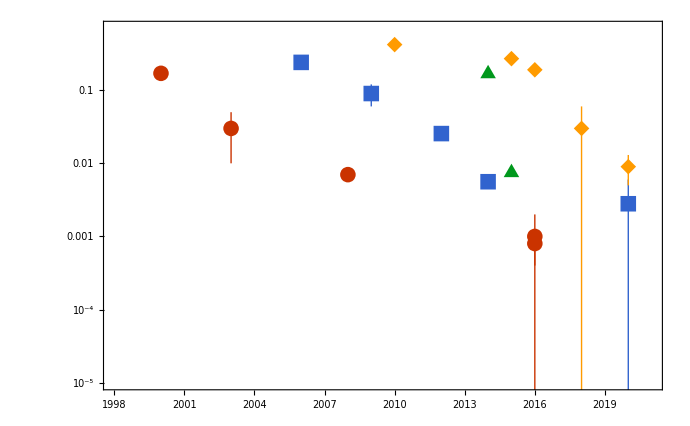

```mathematica
ListLogPlot[{ionsFidelity,superconductingFidelity, rydbergsFidelity, diamondFidelity},PlotRange->{{1998,2021},{10^-5,0.7}},GridLines->{{},{10^-1,10^-2,10^-3,10^-4}},GridLinesStyle->Directive[Dashed],PlotMarkers->{Automatic,16}]
```

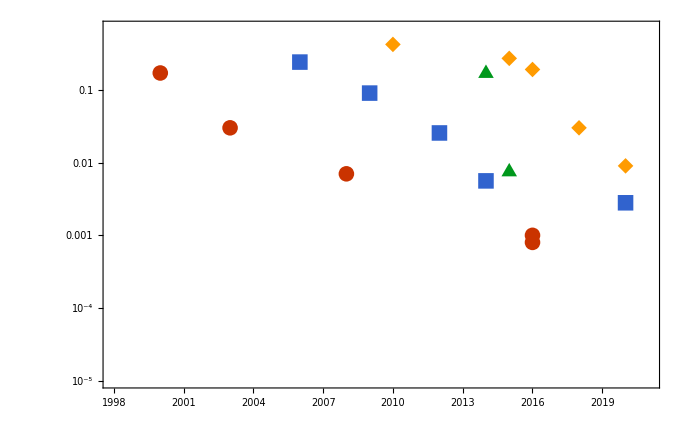

```mathematica
ListLogPlot[{ionsFidelityMean,superconductingFidelityMean, rydbergsFidelityMean, diamondFidelityMean},PlotRange->{{1998,2021},{10^-5,0.7}},GridLines->{{},{10^-1,10^-2,10^-3,10^-4}},GridLinesStyle->Directive[Dashed],PlotMarkers->{Automatic,16}]
```

```mathematica
ionImage =-Graphics- ;
```

```mathematica
ionImage= RemoveBackground[ionImage,{"Background",White}];
```

```mathematica
superconductingImage = -Graphics-;
```

```mathematica
superconductingImage= RemoveBackground[superconductingImage,{"Background",White}];
```

```mathematica
ionsFidelityMean = {#[[1]],#[[2]]}& /@ions;
superconductingFidelityMean=  {#[[1]],#[[2]]}& /@superconductingData;
rydbergsFidelityMean =  {#[[1]],#[[2]]}& /@rydbergsData;
diamondFidelityMean =  {#[[1]],#[[2]]}& /@diamondData;
```

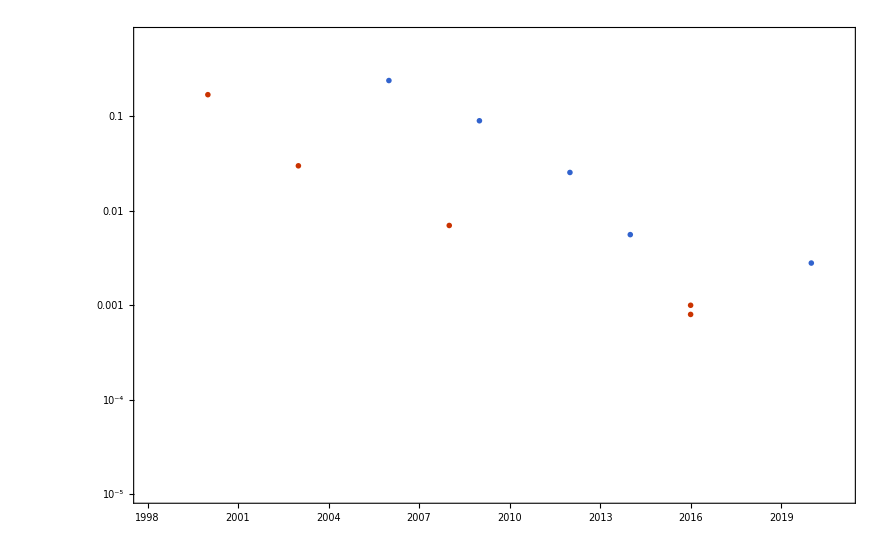

```mathematica
ListLogPlot[{ionsFidelityMean,superconductingFidelityMean},PlotRange->{{1998,2021},{10^-5,0.7}},GridLines->{{},{10^-1,10^-2,10^-3,10^-4}},GridLinesStyle->Directive[Dashed],PlotMarkers -> {{ionImage,30}, {superconductingImage,50}}]
```

```mathematica
ionsLabels= #[[4]]& /@ions;
superconductingLabels= #[[4]]& /@superconductingData;
```

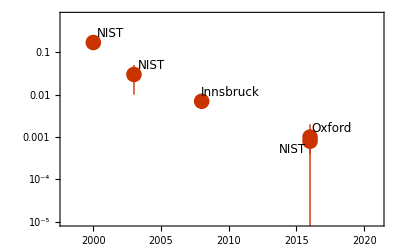

```mathematica
ListLogPlot[MapThread[Labeled[#1,#2]&,{ionsFidelity,ionsLabels}],PlotRange->{{1998,2021},{10^-5,0.7}},GridLines->{{},{10^-1,10^-2,10^-3,10^-4}},GridLinesStyle->Directive[Dashed],PlotMarkers->{Automatic,16}]
```

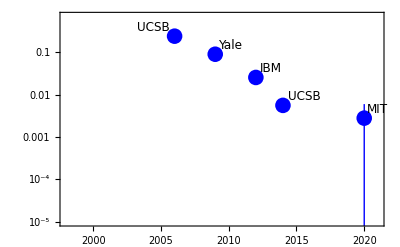

```mathematica
ListLogPlot[MapThread[Labeled[#1,#2]&,{superconductingFidelity,superconductingLabels}],PlotRange->{{1998,2021},{10^-5,0.7}},GridLines->{{},{10^-1,10^-2,10^-3,10^-4}},GridLinesStyle->Directive[Dashed],PlotStyle->Blue,PlotMarkers->{Automatic,16}]
```